# Recursive Komplexity Analysis

## Importing Probability Amplitudes

### L=5 periodic boundary conditions

```mathematica
ACL5Psx1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_sxMode1.m.gz"]][[4]];
```

```mathematica
ACL5Psx12=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_2site_sx12.m.gz"]][[4]];
```

```mathematica
ACL5Psx123=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_3site_sx123.m.gz"]][[4]];
```

```mathematica
ACL5Psx1234=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_4site_sx1234.m.gz"]][[4]];
```

```mathematica
ACL5Psx12345=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_5site_sx12345.m.gz"]][[4]];
```

```mathematica
ACL5Psxtosy=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_sxtosyPiby4.m.gz"]][[4]];
```

```mathematica
ACL5Psy1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_syMode1.m.gz"]][[4]];
```

```mathematica
ACL5Psy12=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_2site_sy12.m.gz"]][[4]];
```

```mathematica
ACL5Psy123=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_3site_sy123.m.gz"]][[4]];
```

```mathematica
ACL5Psy1234=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_4site_sy1234.m.gz"]][[4]];
```

```mathematica
ACL5Psy12345=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_5site_sy12345.m.gz"]][[4]];
```

```mathematica
ACL5Psztosy=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_sztosyPiby4.m.gz"]][[4]];
```

```mathematica
ACL5Psz1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_szMode1.m.gz"]][[4]];
```

```mathematica
ACL5Psz12=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_2site_sz12.m.gz"]][[4]];
```

```mathematica
ACL5Psz123=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_3site_sz123.m.gz"]][[4]];
```

```mathematica
ACL5Psz1234=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_4site_sz1234.m.gz"]][[4]];
```

```mathematica
ACL5Pcc1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_ccMode1.txt"]][[4]];
```

```mathematica
ACL5Pcc2=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_ccMode2.txt"]][[4]];
```

```mathematica
ACL5Pcc3=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_ccMode3.txt"]][[4]];
```

```mathematica
ACL5Pcc4=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_ccMode4.txt"]][[4]];
```

```mathematica
ACL5Pcc5=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_ccMode5.txt"]][[4]];
```

```mathematica
ACL5Psm1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_smMode1.m.gz"]][[4]];
```

```mathematica
ACL5Psp1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_spMode1.txt"]][[4]];
```

```mathematica
ACL5Psp12=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_2site_sp12.txt"]][[4]];
```

```mathematica
ACL5Psp123=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_3site_sp123.txt"]][[4]];
```

```mathematica
ACL5Psp1234=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_4site_sp1234.txt"]][[4]];
```

```mathematica
ACL5Psp12345=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_5site_sp12345.txt"]][[4]];
```

```mathematica
ACL5PRNH1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_RanNormHerm1.m.gz"]][[4]];
```

```mathematica
ACL5PRNH12=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_2site_RanNormHerm12.m.gz"]][[4]];
```

```mathematica
ACL5PRNH123=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_3site_RanNormHerm123.m.gz"]][[4]];
```

```mathematica
ACL5PRNH1234=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_4site_RanNormHerm1234.m.gz"]][[4]];
```

```mathematica
ACL5PRNH12345=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_5site_RanNormHerm12345.m.gz"]][[4]];
```

```mathematica
ACL5PRN1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_RanNorm1.m.gz"]][[4]];
```

```mathematica
ACL5PRN12=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_2site_RanNorm12.m.gz"]][[4]];
```

```mathematica
ACL5PRN123=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_3site_RanNorm123.m.gz"]][[4]];
```

```mathematica
ACL5PRN1234=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_4site_RanNorm1234.m.gz"]][[4]];
```

```mathematica
ACL5PRN12345=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_periodic_5site_RanNorm12345.m.gz"]][[4]];
```

### L=5 open boundary conditions

```mathematica
ACL5sz1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_szMode1.m.gz"]][[4]];
```

```mathematica
ACL5sz2=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_szMode2.m.gz"]][[4]];
```

```mathematica
ACL5sz3=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_szMode3.m.gz"]][[4]];
```

```mathematica
ACL5sz4=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_szMode4.m.gz"]][[4]];
```

```mathematica
ACL5sz5=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_szMode5.m.gz"]][[4]];
```

```mathematica
ACL5sz12=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_2site_sz12.m.gz"]][[4]];
```

```mathematica
ACL5sz123=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_3site_sz123.m.gz"]][[4]];
```

```mathematica
ACL5sz1234=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_4site_sz1234.m.gz"]][[4]];
```

```mathematica
ACL5cc1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_ccMode1.m.gz"]][[4]];
```

```mathematica
ACL5cc2=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_ccMode2.m.gz"]][[4]];
```

```mathematica
ACL5cc3=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_ccMode3.m.gz"]][[4]];
```

```mathematica
ACL5cc4=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_ccMode4.m.gz"]][[4]];
```

```mathematica
ACL5cc5=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_ccMode5.m.gz"]][[4]];
```

```mathematica
ACL5sp1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_spMode1.m.gz"]][[4]];
```

```mathematica
ACL5sp2=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_spMode2.m.gz"]][[4]];
```

```mathematica
ACL5sp3=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_spMode3.m.gz"]][[4]];
```

```mathematica
ACL5sp4=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_spMode4.m.gz"]][[4]];
```

```mathematica
ACL5sp5=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_spMode5.m.gz"]][[4]];
```

```mathematica
ACL5sp12=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_2site_sp12.m.gz"]][[4]];
```

```mathematica
ACL5sp123=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_3site_sp123.m.gz"]][[4]];
```

```mathematica
ACL5sp1234=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_4site_sp1234.m.gz"]][[4]];
```

```mathematica
ACL5sp12345=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_5site_sp12345.m.gz"]][[4]];
```

```mathematica
ACL5RN1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_RanNorm1.m.gz"]][[4]];
```

```mathematica
ACL5RN2=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_RanNorm2.m.gz"]][[4]];
```

```mathematica
ACL5RN3=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_RanNorm3.m.gz"]][[4]];
```

```mathematica
ACL5RN4=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_RanNorm4.m.gz"]][[4]];
```

```mathematica
ACL5RN5=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_RanNorm5.m.gz"]][[4]];
```

```mathematica
ACL5RN12=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_2site_RanNorm12.m.gz"]][[4]];
```

```mathematica
ACL5RN123=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_3site_RanNorm123.m.gz"]][[4]];
```

```mathematica
ACL5RN1234=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_4site_RanNorm1234.m.gz"]][[4]];
```

```mathematica
ACL5RN12345=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_5site_RanNorm12345.m.gz"]][[4]];
```

```mathematica
ACL5RNH1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_RanNormHerm1.m.gz"]][[4]];
```

```mathematica
ACL5RNH2=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_RanNormHerm2.m.gz"]][[4]];
```

```mathematica
ACL5RNH3=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_RanNormHerm3.m.gz"]][[4]];
```

```mathematica
ACL5RNH4=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_RanNormHerm4.m.gz"]][[4]];
```

```mathematica
ACL5RNH5=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_RanNormHerm5.m.gz"]][[4]];
```

```mathematica
ACL5RNH12=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_2site_RanNormHerm12.m.gz"]][[4]];
```

```mathematica
ACL5RNH123=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_3site_RanNormHerm123.m.gz"]][[4]];
```

```mathematica
ACL5RNH1234=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_4site_RanNormHerm1234.m.gz"]][[4]];
```

```mathematica
ACL5RNH12345=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAlt_5site_RanNormHerm12345.m.gz"]][[4]];
```

```mathematica
ACL5Ferrocc1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAltFerro_ccMode1.m.gz"]][[4]];
```

```mathematica
ACL5Ferrocc2=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAltFerro_ccMode2.m.gz"]][[4]];
```

```mathematica
ACL5Ferrocc3=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAltFerro_ccMode3.m.gz"]][[4]];
```

```mathematica
ACL5Ferrocc4=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAltFerro_ccMode4.m.gz"]][[4]];
```

```mathematica
ACL5Ferrocc5=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAltFerro_ccMode5.m.gz"]][[4]];
```

```mathematica
ACL5Ferro10cc1=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAltFerro10_ccMode1.m.gz"]][[4]];
```

```mathematica
ACL5Ferro10cc2=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAltFerro10_ccMode2.m.gz"]][[4]];
```

```mathematica
ACL5Ferro10cc3=ToExpression[Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5TFIMAltFerro10_ccMode3.m.gz"]][[4]];
```

## Parameters

```mathematica
tMax=100;
tPts=500;
Prec=200;
tVals = Table[N[tMax*(i)/(tPts),Prec], {i, 1, tPts}];
```

```mathematica
FrameSpecsKt={Frame->{{True,True},{True,True}},FrameLabel->{{"K",None},{"t",None}},FrameTicks->{{True,True},{True,True}},ImageSize->350,AspectRatio->0.67};
```

```mathematica
FrameSpecsKtMulti={Frame->{{True,True},{True,True}},FrameLabel->{{"K",None},{"t",None}},FrameTicks->{{True,True},{True,True}},ImageSize->500,AspectRatio->0.55};
```

## Komplexity for L=5 periodic BCs

### σ^x

```mathematica
cut=Length[ACL5Psx1];
PL5Psx1=Table[{tVals[[j]],Total[Abs[ACL5Psx1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psx1=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psx1[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psx12];
PL5Psx12=Table[{tVals[[j]],Total[Abs[ACL5Psx12[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psx12=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psx12[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psx123];
PL5Psx123=Table[{tVals[[j]],Total[Abs[ACL5Psx123[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psx123=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psx123[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psx1234];
PL5Psx1234=Table[{tVals[[j]],Total[Abs[ACL5Psx1234[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psx1234=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psx1234[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psx12345];
PL5Psx12345=Table[{tVals[[j]],Total[Abs[ACL5Psx12345[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psx12345=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psx12345[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psxtosy];
PL5Psxtosy=Table[{tVals[[j]],Total[Abs[ACL5Psxtosy[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psxtosy=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psxtosy[[2;;cut,j]]]^2},{j,1,tPts}];
```

### σ^y

```mathematica
cut=Length[ACL5Psy1];
PL5Psy1=Table[{tVals[[j]],Total[Abs[ACL5Psy1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psy1=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psy1[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psy12];
PL5Psy12=Table[{tVals[[j]],Total[Abs[ACL5Psy12[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psy12=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psy12[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psy123];
PL5Psy123=Table[{tVals[[j]],Total[Abs[ACL5Psy123[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psy123=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psy123[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psy1234];
PL5Psy1234=Table[{tVals[[j]],Total[Abs[ACL5Psy1234[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psy1234=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psy1234[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psy12345];
PL5Psy12345=Table[{tVals[[j]],Total[Abs[ACL5Psy12345[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psy12345=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psy12345[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psztosy];
PL5Psztosy=Table[{tVals[[j]],Total[Abs[ACL5Psztosy[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psztosy=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psztosy[[2;;cut,j]]]^2},{j,1,tPts}];
```

### σ^z

```mathematica
cut=Length[ACL5Psz1];
PL5Psz1=Table[{tVals[[j]],Total[Abs[ACL5Psz1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psz1=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psz1[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psz12];
PL5Psz12=Table[{tVals[[j]],Total[Abs[ACL5Psz12[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psz12=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psz12[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psz123];
PL5Psz123=Table[{tVals[[j]],Total[Abs[ACL5Psz123[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psz123=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psz123[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psz1234];
PL5Psz1234=Table[{tVals[[j]],Total[Abs[ACL5Psz1234[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psz1234=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psz1234[[2;;cut,j]]]^2},{j,1,tPts}];
```

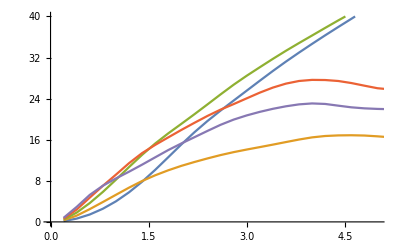

```mathematica
ListLinePlot[{KL5Psx1, KL5Psx12,KL5Psx123,KL5Psx1234,KL5Psx12345}, PlotRange->{{0,5},{0,40}}]
```

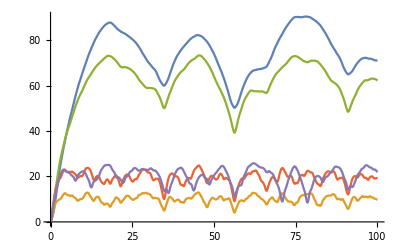

```mathematica
ListLinePlot[{KL5Psy1,KL5Psy12,KL5Psy123,KL5Psy1234,KL5Psy12345}]
```

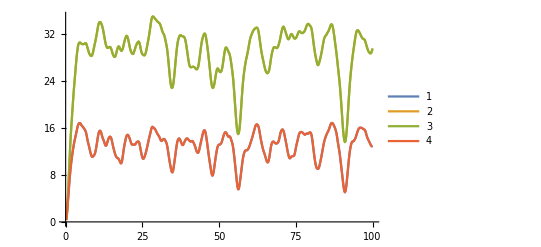

```mathematica
ListLinePlot[{KL5Psz1,KL5Psz12, KL5Psz123, KL5Psz1234}, PlotLegends->Automatic]
```

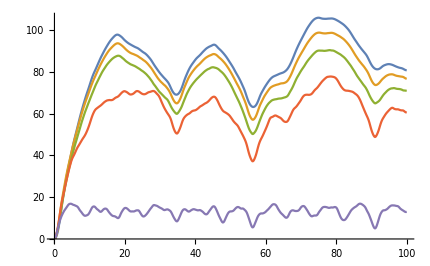

```mathematica
ListLinePlot[{KL5Psx1,KL5Psxtosy,KL5Psy1,KL5Psztosy,KL5Psz1}]
```

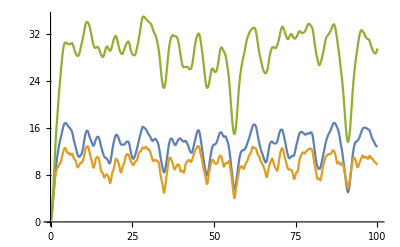

```mathematica
ListLinePlot[{KL5Psx12,KL5Psy12,KL5Psz12}]
```

### J-W operators

```mathematica
cut=Length[ACL5Pcc1];
PL5Pcc1=Table[{tVals[[j]],Total[Abs[ACL5Pcc1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Pcc1=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Pcc1[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Pcc2];
PL5Pcc2=Table[{tVals[[j]],Total[Abs[ACL5Pcc2[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Pcc2=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Pcc2[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Pcc3];
PL5Pcc3=Table[{tVals[[j]],Total[Abs[ACL5Pcc3[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Pcc3=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Pcc3[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Pcc4];
PL5Pcc4=Table[{tVals[[j]],Total[Abs[ACL5Pcc4[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Pcc4=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Pcc4[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Pcc5];
PL5Pcc5=Table[{tVals[[j]],Total[Abs[ACL5Pcc5[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Pcc5=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Pcc5[[2;;cut,j]]]^2},{j,1,tPts}];
```

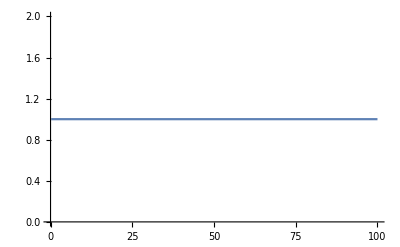

```mathematica
ListLinePlot[PL5Pcc5]
```

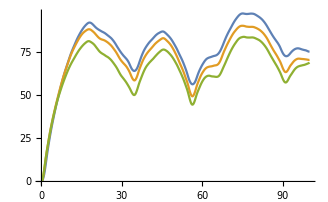

```mathematica
ListLinePlot[{KL5Pcc1,KL5Pcc2,KL5Pcc3}]
```

### σ^+ operators

```mathematica
cut=Length[ACL5Psm1];
PL5Psm1=Table[{tVals[[j]],Total[Abs[ACL5Psm1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psm1=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psm1[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psp1];
PL5Psp1=Table[{tVals[[j]],Total[Abs[ACL5Psp1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psp1=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psp1[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psp12];
PL5Psp12=Table[{tVals[[j]],Total[Abs[ACL5Psp12[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psp12=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psp12[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psp123];
PL5Psp123=Table[{tVals[[j]],Total[Abs[ACL5Psp123[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psp123=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psp123[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psp1234];
PL5Psp1234=Table[{tVals[[j]],Total[Abs[ACL5Psp1234[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psp1234=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psp1234[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Psp12345];
PL5Psp12345=Table[{tVals[[j]],Total[Abs[ACL5Psp12345[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Psp12345=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Psp12345[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
ListLinePlot[PL5Psp12345]
```

-Graphics-

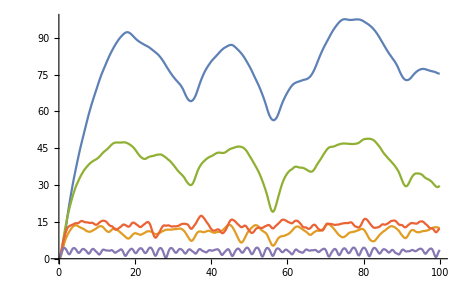

```mathematica
ListLinePlot[{KL5Psp1,KL5Psp12,KL5Psp123,KL5Psp1234,KL5Psp12345}]
```

### Random Normalized Hermitian operators

```mathematica
cut=Length[ACL5PRNH1];
PL5PRNH1=Table[{tVals[[j]],Total[Abs[ACL5PRNH1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5PRNH1=Table[{tVals[[j]],Range[cut-1].Abs[ACL5PRNH1[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5PRNH12];
PL5PRNH12=Table[{tVals[[j]],Total[Abs[ACL5PRNH12[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5PRNH12=Table[{tVals[[j]],Range[cut-1].Abs[ACL5PRNH12[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5PRNH123];
PL5PRNH123=Table[{tVals[[j]],Total[Abs[ACL5PRNH123[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5PRNH123=Table[{tVals[[j]],Range[cut-1].Abs[ACL5PRNH123[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5PRNH1234];
PL5PRNH1234=Table[{tVals[[j]],Total[Abs[ACL5PRNH1234[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5PRNH1234=Table[{tVals[[j]],Range[cut-1].Abs[ACL5PRNH1234[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5PRNH12345];
PL5PRNH12345=Table[{tVals[[j]],Total[Abs[ACL5PRNH12345[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5PRNH12345=Table[{tVals[[j]],Range[cut-1].Abs[ACL5PRNH12345[[2;;cut,j]]]^2},{j,1,tPts}];
```

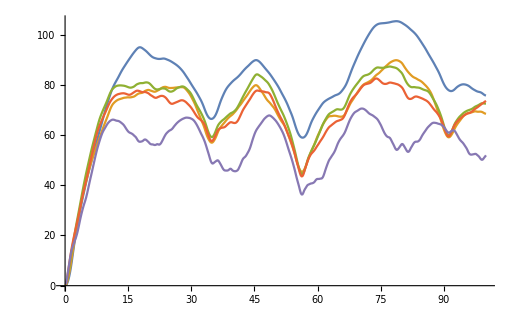

```mathematica
x=ListLinePlot[{KL5PRNH1,KL5PRNH12,KL5PRNH123, KL5PRNH1234, KL5PRNH12345},PlotRange->{{0,100},Automatic}]
```

```mathematica
Rasterize[x,RasterSize->1200]
```

-Graphics-

### Random Normalized Matrices

```mathematica
cut=Length[ACL5PRN1];
PL5PRN1=Table[{tVals[[j]],Total[Abs[ACL5PRN1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5PRN1=Table[{tVals[[j]],Range[cut-1].Abs[ACL5PRN1[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5PRN12];
PL5PRN12=Table[{tVals[[j]],Total[Abs[ACL5PRN12[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5PRN12=Table[{tVals[[j]],Range[cut-1].Abs[ACL5PRN12[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5PRN123];
PL5PRN123=Table[{tVals[[j]],Total[Abs[ACL5PRN123[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5PRN123=Table[{tVals[[j]],Range[cut-1].Abs[ACL5PRN123[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5PRN1234];
PL5PRN1234=Table[{tVals[[j]],Total[Abs[ACL5PRN1234[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5PRN1234=Table[{tVals[[j]],Range[cut-1].Abs[ACL5PRN1234[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5PRN12345];
PL5PRN12345=Table[{tVals[[j]],Total[Abs[ACL5PRN12345[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5PRN12345=Table[{tVals[[j]],Range[cut-1].Abs[ACL5PRN12345[[2;;cut,j]]]^2},{j,1,tPts}];
```

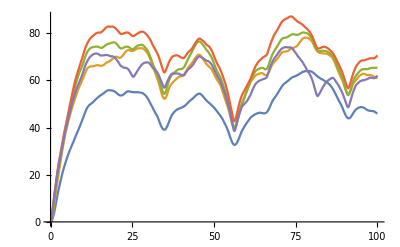

```mathematica
ListLinePlot[{KL5PRN1,KL5PRN12,KL5PRN123, KL5PRN1234, KL5PRN12345},PlotRange->{{0,100},Automatic}]
```

## Komplexity for L=5 Open BCs

### σ^z

```mathematica
cut=Length[ACL5sz1];
PL5sz1=Table[{tVals[[j]],Total[Abs[ACL5sz1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5sz1=Table[{tVals[[j]],Range[cut-1].Abs[ACL5sz1[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5sz2];
PL5sz2=Table[{tVals[[j]],Total[Abs[ACL5sz2[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5sz2=Table[{tVals[[j]],Range[cut-1].Abs[ACL5sz2[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5sz3];
PL5sz3=Table[{tVals[[j]],Total[Abs[ACL5sz3[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5sz3=Table[{tVals[[j]],Range[cut-1].Abs[ACL5sz3[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5sz4];
PL5sz4=Table[{tVals[[j]],Total[Abs[ACL5sz4[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5sz4=Table[{tVals[[j]],Range[cut-1].Abs[ACL5sz4[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5sz5];
PL5sz5=Table[{tVals[[j]],Total[Abs[ACL5sz5[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5sz5=Table[{tVals[[j]],Range[cut-1].Abs[ACL5sz5[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5sz12];
PL5sz12=Table[{tVals[[j]],Total[Abs[ACL5sz12[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5sz12=Table[{tVals[[j]],Range[cut-1].Abs[ACL5sz12[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5sz123];
PL5sz123=Table[{tVals[[j]],Total[Abs[ACL5sz123[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5sz123=Table[{tVals[[j]],Range[cut-1].Abs[ACL5sz123[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5sz1234];
PL5sz1234=Table[{tVals[[j]],Total[Abs[ACL5sz1234[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5sz1234=Table[{tVals[[j]],Range[cut-1].Abs[ACL5sz1234[[2;;cut,j]]]^2},{j,1,tPts}];
```

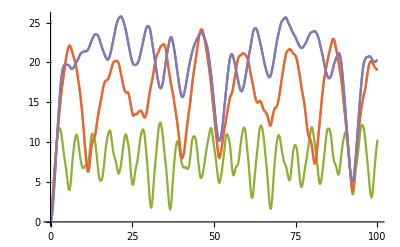

```mathematica
ListLinePlot[{KL5sz1, KL5sz2, KL5sz3, KL5sz4, KL5sz5}]
```

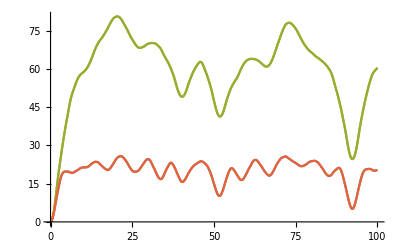

```mathematica
ListLinePlot[{KL5sz1,KL5sz12, KL5sz123, KL5sz1234}]
```

### J-W operators

```mathematica
cut=Length[ACL5cc1];
PL5cc1=Table[{tVals[[j]],Total[Abs[ACL5cc1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5cc1=Table[{tVals[[j]],Range[cut-1].Abs[ACL5cc1[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5cc2];
PL5cc2=Table[{tVals[[j]],Total[Abs[ACL5cc2[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5cc2=Table[{tVals[[j]],Range[cut-1].Abs[ACL5cc2[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5cc3];
PL5cc3=Table[{tVals[[j]],Total[Abs[ACL5cc3[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5cc3=Table[{tVals[[j]],Range[cut-1].Abs[ACL5cc3[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5cc4];
PL5cc4=Table[{tVals[[j]],Total[Abs[ACL5cc4[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5cc4=Table[{tVals[[j]],Range[cut-1].Abs[ACL5cc4[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5cc5];
PL5cc5=Table[{tVals[[j]],Total[Abs[ACL5cc5[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5cc5=Table[{tVals[[j]],Range[cut-1].Abs[ACL5cc5[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
ListLinePlot[PL5cc1]
```

-Graphics-

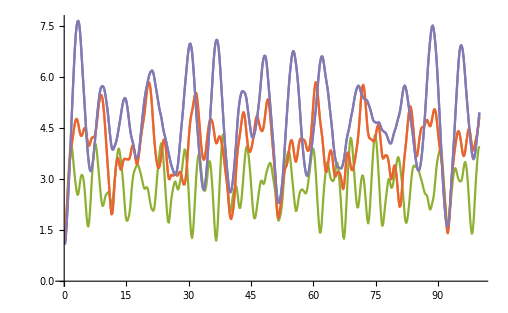

```mathematica
ListLinePlot[{KL5cc1, KL5cc2, KL5cc3, KL5cc4, KL5cc5}]
```

### σ^+ operators

```mathematica
cut=Length[ACL5sp1]
PL5sp1=Table[{tVals[[j]],Total[Abs[ACL5sp1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5sp1=Table[{tVals[[j]],Range[cut-1].Abs[ACL5sp1[[2;;cut,j]]]^2},{j,1,tPts}];
```

10

```mathematica
cut=Length[ACL5sp2]
PL5sp2=Table[{tVals[[j]],Total[Abs[ACL5sp2[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5sp2=Table[{tVals[[j]],Range[cut-1].Abs[ACL5sp2[[2;;cut,j]]]^2},{j,1,tPts}];
```

90

```mathematica
cut=Length[ACL5sp3];
PL5sp3=Table[{tVals[[j]],Total[Abs[ACL5sp3[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5sp3=Table[{tVals[[j]],Range[cut-1].Abs[ACL5sp3[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5sp4];
PL5sp4=Table[{tVals[[j]],Total[Abs[ACL5sp4[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5sp4=Table[{tVals[[j]],Range[cut-1].Abs[ACL5sp4[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5sp5];
PL5sp5=Table[{tVals[[j]],Total[Abs[ACL5sp5[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5sp5=Table[{tVals[[j]],Range[cut-1].Abs[ACL5sp5[[2;;cut,j]]]^2},{j,1,tPts}];
```

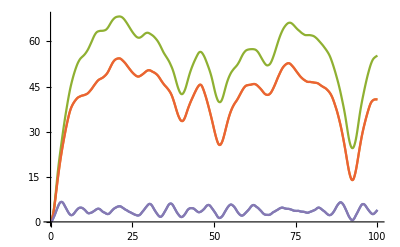

```mathematica
ListLinePlot[{KL5sp1, KL5sp2, KL5sp3, KL5sp4, KL5sp5}]
```

```mathematica
cut=Length[ACL5sp12];
PL5sp12=Table[{tVals[[j]],Total[Abs[ACL5sp12[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5sp12=Table[{tVals[[j]],Range[cut-1].Abs[ACL5sp12[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5sp123];
PL5sp123=Table[{tVals[[j]],Total[Abs[ACL5sp123[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5sp123=Table[{tVals[[j]],Range[cut-1].Abs[ACL5sp123[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5sp1234];
PL5sp1234=Table[{tVals[[j]],Total[Abs[ACL5sp1234[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5sp1234=Table[{tVals[[j]],Range[cut-1].Abs[ACL5sp1234[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5sp12345];
PL5sp12345=Table[{tVals[[j]],Total[Abs[ACL5sp12345[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5sp12345=Table[{tVals[[j]],Range[cut-1].Abs[ACL5sp12345[[2;;cut,j]]]^2},{j,1,tPts}];
```

### Random Normed matrices

```mathematica
cut=Length[ACL5RN1];
PL5RN1=Table[{tVals[[j]],Total[Abs[ACL5RN1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5RN1=Table[{tVals[[j]],Range[cut-1].Abs[ACL5RN1[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5RN2];
PL5RN2=Table[{tVals[[j]],Total[Abs[ACL5RN2[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5RN2=Table[{tVals[[j]],Range[cut-1].Abs[ACL5RN2[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5RN3];
PL5RN3=Table[{tVals[[j]],Total[Abs[ACL5RN3[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5RN3=Table[{tVals[[j]],Range[cut-1].Abs[ACL5RN3[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5RN4];
PL5RN4=Table[{tVals[[j]],Total[Abs[ACL5RN4[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5RN4=Table[{tVals[[j]],Range[cut-1].Abs[ACL5RN4[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5RN5];
PL5RN5=Table[{tVals[[j]],Total[Abs[ACL5RN5[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5RN5=Table[{tVals[[j]],Range[cut-1].Abs[ACL5RN5[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5RN12];
PL5RN12=Table[{tVals[[j]],Total[Abs[ACL5RN12[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5RN12=Table[{tVals[[j]],Range[cut-1].Abs[ACL5RN12[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5RN123];
PL5RN123=Table[{tVals[[j]],Total[Abs[ACL5RN123[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5RN123=Table[{tVals[[j]],Range[cut-1].Abs[ACL5RN123[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5RN1234];
PL5RN1234=Table[{tVals[[j]],Total[Abs[ACL5RN1234[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5RN1234=Table[{tVals[[j]],Range[cut-1].Abs[ACL5RN1234[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5RN12345];
PL5RN12345=Table[{tVals[[j]],Total[Abs[ACL5RN12345[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5RN12345=Table[{tVals[[j]],Range[cut-1].Abs[ACL5RN12345[[2;;cut,j]]]^2},{j,1,tPts}];
```

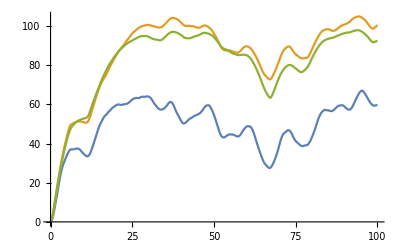

```mathematica
ListLinePlot[{KL5RN12, KL5RN123, KL5RN1234}]
```

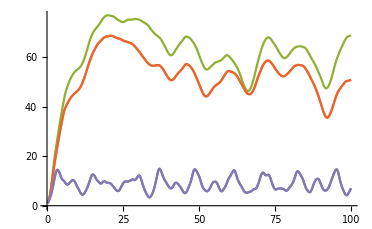

```mathematica
ListLinePlot[{KL5RN1, KL5RN2, KL5RN3,KL5RN4, KL5RN5}]
```

### Random Normed Hermitian matrices

```mathematica
cut=Length[ACL5RNH1];
PL5RNH1=Table[{tVals[[j]],Total[Abs[ACL5RNH1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5RNH1=Table[{tVals[[j]],Range[cut-1].Abs[ACL5RNH1[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5RNH2];
PL5RNH2=Table[{tVals[[j]],Total[Abs[ACL5RNH2[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5RNH2=Table[{tVals[[j]],Range[cut-1].Abs[ACL5RNH2[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5RNH3];
PL5RNH3=Table[{tVals[[j]],Total[Abs[ACL5RNH3[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5RNH3=Table[{tVals[[j]],Range[cut-1].Abs[ACL5RNH3[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5RNH4];
PL5RNH4=Table[{tVals[[j]],Total[Abs[ACL5RNH4[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5RNH4=Table[{tVals[[j]],Range[cut-1].Abs[ACL5RNH4[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5RNH5];
PL5RNH5=Table[{tVals[[j]],Total[Abs[ACL5RNH5[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5RNH5=Table[{tVals[[j]],Range[cut-1].Abs[ACL5RNH5[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5RNH12];
PL5RNH12=Table[{tVals[[j]],Total[Abs[ACL5RNH12[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5RNH12=Table[{tVals[[j]],Range[cut-1].Abs[ACL5RNH12[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5RNH123];
PL5RNH123=Table[{tVals[[j]],Total[Abs[ACL5RNH123[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5RNH123=Table[{tVals[[j]],Range[cut-1].Abs[ACL5RNH123[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5RNH1234];
PL5RNH1234=Table[{tVals[[j]],Total[Abs[ACL5RNH1234[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5RNH1234=Table[{tVals[[j]],Range[cut-1].Abs[ACL5RNH1234[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5RNH12345];
PL5RNH12345=Table[{tVals[[j]],Total[Abs[ACL5RNH12345[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5RNH12345=Table[{tVals[[j]],Range[cut-1].Abs[ACL5RNH12345[[2;;cut,j]]]^2},{j,1,tPts}];
```

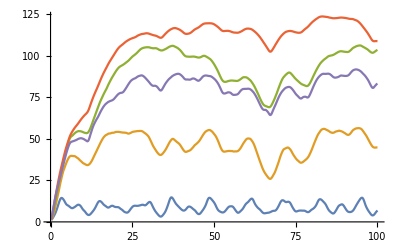

```mathematica
ListLinePlot[{KL5RNH1,KL5RNH12, KL5RNH123, KL5RNH1234, KL5RNH12345}]
```

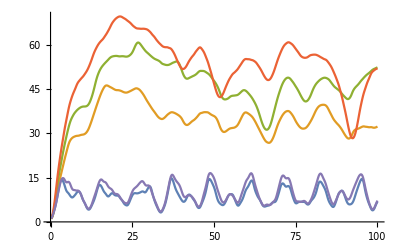

```mathematica
ListLinePlot[{KL5RNH1, KL5RNH2, KL5RNH3,KL5RNH4, KL5RNH5}]
```

### Ferromagnetic phase

```mathematica
cut=Length[ACL5Ferrocc1]-1;
PL5Ferrocc1=Table[{tVals[[j]],Total[Abs[ACL5Ferrocc1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Ferrocc1=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Ferrocc1[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Ferrocc2]-1;
PL5Ferrocc2=Table[{tVals[[j]],Total[Abs[ACL5Ferrocc2[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Ferrocc2=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Ferrocc2[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Ferrocc3]-1;
PL5Ferrocc3=Table[{tVals[[j]],Total[Abs[ACL5Ferrocc3[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Ferrocc3=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Ferrocc3[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Ferrocc4]-1;
PL5Ferrocc4=Table[{tVals[[j]],Total[Abs[ACL5Ferrocc4[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Ferrocc4=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Ferrocc4[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Ferrocc5]-1;
PL5Ferrocc5=Table[{tVals[[j]],Total[Abs[ACL5Ferrocc5[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Ferrocc5=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Ferrocc5[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Ferro10cc1];
PL5Ferro10cc1=Table[{tVals[[j]],Total[Abs[ACL5Ferro10cc1[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Ferro10cc1=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Ferro10cc1[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Ferro10cc2]-1;
PL5Ferro10cc2=Table[{tVals[[j]],Total[Abs[ACL5Ferro10cc2[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Ferro10cc2=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Ferro10cc2[[2;;cut,j]]]^2},{j,1,tPts}];
```

```mathematica
cut=Length[ACL5Ferro10cc3]-1;
PL5Ferro10cc3=Table[{tVals[[j]],Total[Abs[ACL5Ferro10cc3[[1;;cut,j]]]^2]},{j,1,tPts}];
KL5Ferro10cc3=Table[{tVals[[j]],Range[cut-1].Abs[ACL5Ferro10cc3[[2;;cut,j]]]^2},{j,1,tPts}];
```

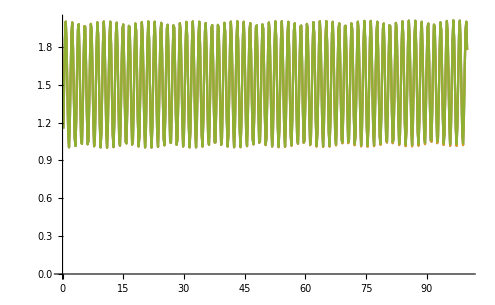

```mathematica
ListLinePlot[{ KL5Ferrocc1, KL5Ferrocc2, KL5Ferrocc3}]
```

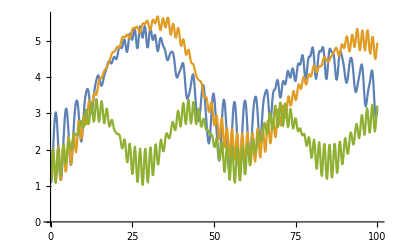

```mathematica
ListLinePlot[{KL5Ferro10cc1,KL5Ferro10cc2,KL5Ferro10cc3}]
```

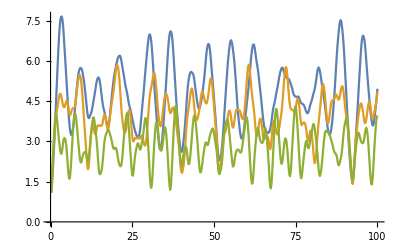

```mathematica
ListLinePlot[{KL5cc1, KL5cc2, KL5cc3}]
```

## Periodic Comparisons

### Comparing Pauli operators

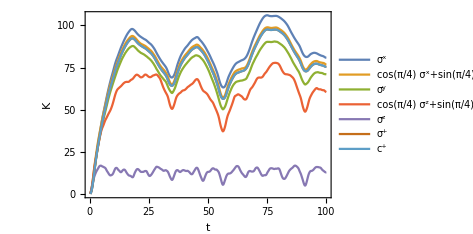

```mathematica
ListLinePlot[{KL5Psx1,KL5Psxtosy,KL5Psy1,KL5Psztosy,KL5Psz1, KL5Psp1, KL5Pcc1},AxesLabel->{"t","K"}, PlotLegends->Placed[{
Style[ ToExpression["(\\sigma)^x", TeXForm, HoldForm], Small],
Style[ ToExpression["\\cos(\\pi/4)\\sigma^x +  \\sin(\\pi/4) \\sigma^y", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma)^y", TeXForm, HoldForm], Small],
Style[ ToExpression["\\cos(\\pi/4)\\sigma^z +  \\sin(\\pi/4) \\sigma^y", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma)^z", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma)^+", TeXForm, HoldForm], Small],Style[ ToExpression["(c)^+", TeXForm, HoldForm], Small]
},Right],
Evaluate@Sequence@@FrameSpecsKt]
```

```mathematica
Rasterize[%,RasterSize->1300]
```

-Graphics-

### Comparing J-W operators as a function of sites

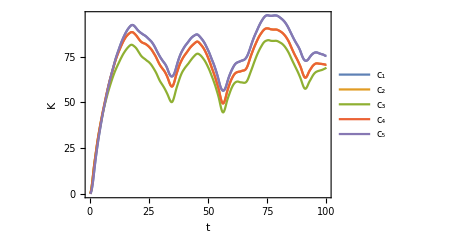

```mathematica
ListLinePlot[{KL5Pcc1,KL5Pcc2,KL5Pcc3,KL5Pcc4,KL5Pcc5},
AxesLabel->{"t","K"}, PlotLegends->Placed[{
Style[ ToExpression["(c)_(1)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c)_(2)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c)_(3)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c)_(4)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c)_(5)", TeXForm, HoldForm], Small]},Right],
Evaluate@Sequence@@FrameSpecsKt]
```

```mathematica
Rasterize[%,RasterSize->1300]
```

-Graphics-

### Comparing multi-site sigma^+ ops as function of sites

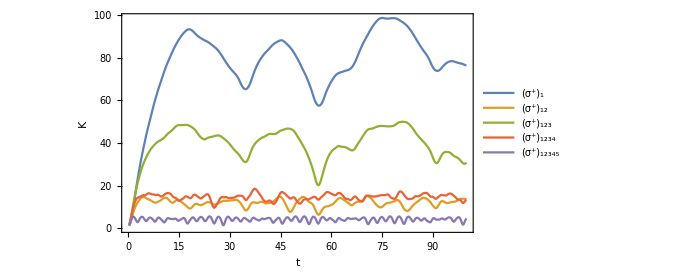

```mathematica
ListLinePlot[{KL5Psp1,KL5Psp12,KL5Psp123,KL5Psp1234, KL5Psp12345},
AxesLabel->{"t","K"}, PlotLegends->Placed[{
Style[ ToExpression["(\\sigma^+)_(1)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(12)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(123)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(1234)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(12345)", TeXForm, HoldForm], Small]},{0.1,0.75}],
Evaluate@Sequence@@FrameSpecsKtMulti]
```

### Comparing multi-site Hermitian random ops as a function of sites

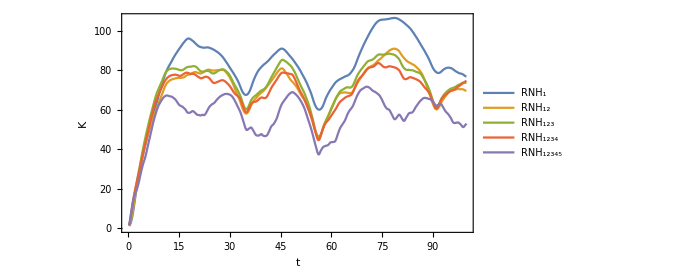

```mathematica
ListLinePlot[{KL5PRNH1,KL5PRNH12, KL5PRNH123, KL5PRNH1234, KL5PRNH12345},
AxesLabel->{"t","K"}, PlotLegends->Placed[{
Style[ ToExpression["(\\Text{RNH})_(1)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\Text{RNH})_(12)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\Text{RNH})_(123)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\Text{RNH})_(1234)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\Text{RNH})_(12345)", TeXForm, HoldForm], Small]},{0.85,0.25}],
Evaluate@Sequence@@FrameSpecsKtMulti]
```

### Comparing multi-site random ops as a function of sites

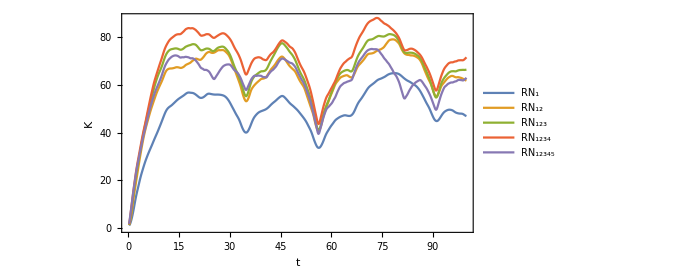

```mathematica
ListLinePlot[{KL5PRN1,KL5PRN12, KL5PRN123, KL5PRN1234, KL5PRN12345},
AxesLabel->{"t","K"}, PlotLegends->Placed[{
Style[ ToExpression["(\\Text{RN})_(1)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\Text{RN})_(12)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\Text{RN})_(123)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\Text{RN})_(1234)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\Text{RN})_(12345)", TeXForm, HoldForm], Small]},{0.85,0.25}],
Evaluate@Sequence@@FrameSpecsKtMulti]
```

### Periodic Multi-site σ^+ vs J-W

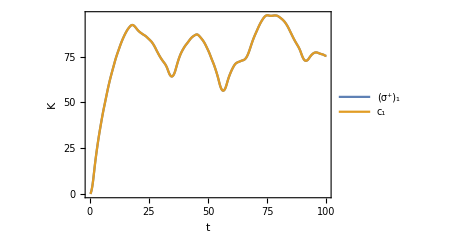

```mathematica
Psp1vsPcc1=ListLinePlot[{KL5Psp1,KL5Pcc1}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(1)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_1", TeXForm, HoldForm], Medium]},{0.8,0.35}],
Evaluate@Sequence@@FrameSpecsKt]
```

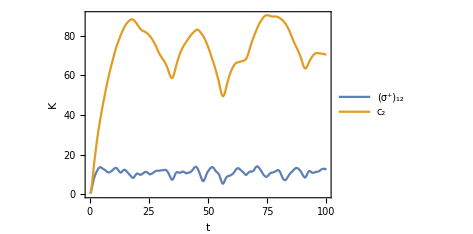

```mathematica
Psp12vsPcc2=ListLinePlot[{KL5Psp12,KL5Pcc2}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(12)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_2", TeXForm, HoldForm], Medium]},{0.8,0.35}],
Evaluate@Sequence@@FrameSpecsKt]
```

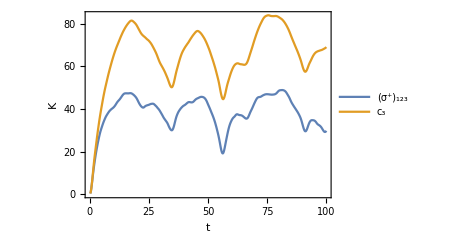

```mathematica
Psp123vsPcc3=ListLinePlot[{KL5Psp123,KL5Pcc3}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(123)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_3", TeXForm, HoldForm], Medium]},{0.8,0.2}],
Evaluate@Sequence@@FrameSpecsKt]
```

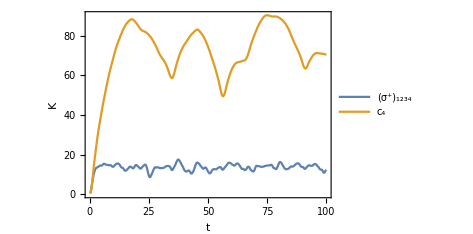

```mathematica
Psp1234vsPcc4=ListLinePlot[{KL5Psp1234,KL5Pcc4}, AxesLabel->{"t","K"},
 PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(1234)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_4", TeXForm, HoldForm], Medium]},{0.8,0.35}],
Evaluate@Sequence@@FrameSpecsKt]
```

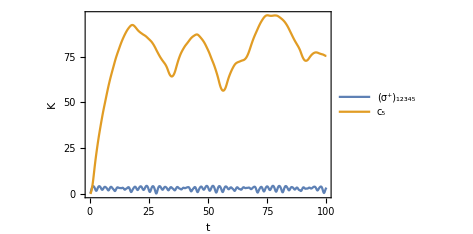

```mathematica
Psp12345vsPcc5=ListLinePlot[{KL5Psp12345,KL5Pcc5}, AxesLabel->{"t","K"},
 PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(12345)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_5", TeXForm, HoldForm], Medium]},{0.8,0.35}],
Evaluate@Sequence@@FrameSpecsKt]
```

### Periodic Multi-site Hermitian random vs J-W

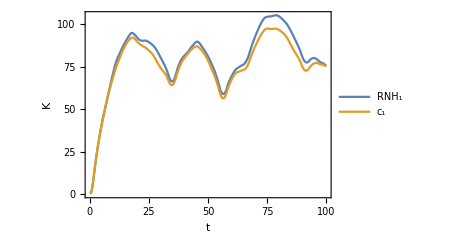

```mathematica
PRNH1vsPcc1=ListLinePlot[{KL5PRNH1,KL5Pcc1}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\Text{RNH})_(1)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_1", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

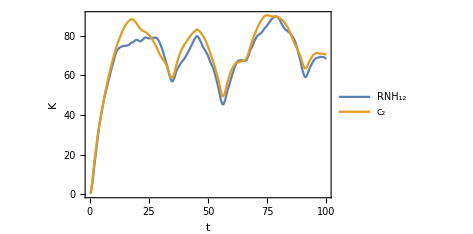

```mathematica
PRNH12vsPcc2=ListLinePlot[{KL5PRNH12,KL5Pcc2}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\Text{RNH})_(12)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_2", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

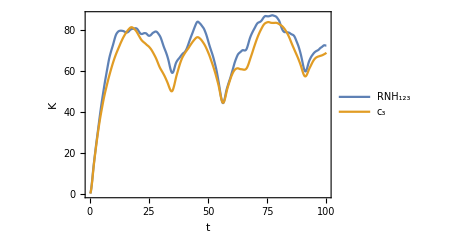

```mathematica
PRNH123vsPcc3=ListLinePlot[{KL5PRNH123,KL5Pcc3}, AxesLabel->{"t","K"}, 
PlotLegends->Placed[{Style[ ToExpression["(\\Text{RNH})_(123)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_3", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

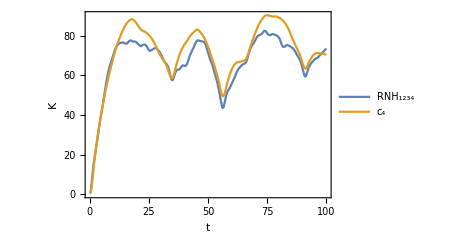

```mathematica
PRNH1234vsPcc4=ListLinePlot[{KL5PRNH1234,KL5Pcc4}, AxesLabel->{"t","K"},
 PlotLegends->Placed[{Style[ ToExpression["(\\Text{RNH})_(1234)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_4", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

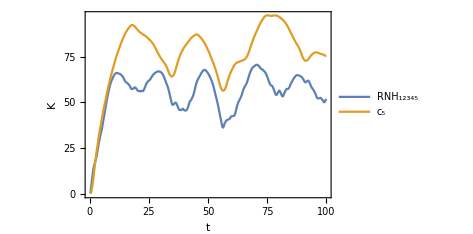

```mathematica
PRNH12345vsPcc5=ListLinePlot[{KL5PRNH12345,KL5Pcc5}, AxesLabel->{"t","K"},
 PlotLegends->Placed[{Style[ ToExpression["\\Text{RNH}_(12345)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_5", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

### Periodic Multi-site random vs J - W

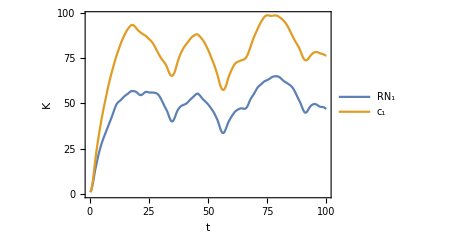

```mathematica
PRN1vsPcc1=ListLinePlot[{KL5PRN1,KL5Pcc1}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\Text{RN})_(1)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_1", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

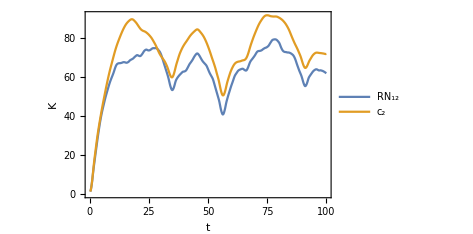

```mathematica
PRN12vsPcc2=ListLinePlot[{KL5PRN12,KL5Pcc2}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\Text{RN})_(12)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_2", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

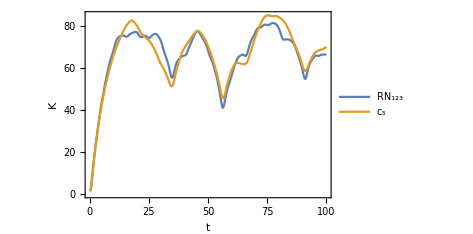

```mathematica
PRN123vsPcc3=ListLinePlot[{KL5PRN123,KL5Pcc3}, AxesLabel->{"t","K"}, 
PlotLegends->Placed[{Style[ ToExpression["(\\Text{RN})_(123)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_3", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

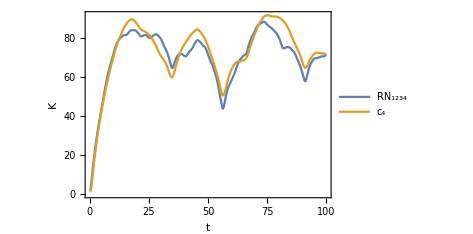

```mathematica
PRN1234vsPcc4=ListLinePlot[{KL5PRN1234,KL5Pcc4}, AxesLabel->{"t","K"},
 PlotLegends->Placed[{Style[ ToExpression["(\\Text{RN})_(1234)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_4", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

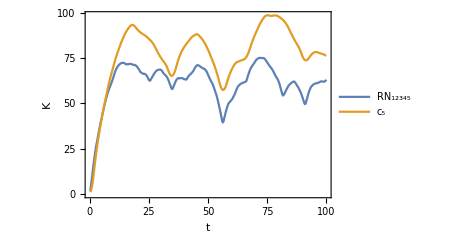

```mathematica
PRN12345vsPcc5=ListLinePlot[{KL5PRN12345,KL5Pcc5}, AxesLabel->{"t","K"},
 PlotLegends->Placed[{Style[ ToExpression["\\Text{RN}_(12345)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_5", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

### Periodic Multi-site random vs Multi-site random Hermitian

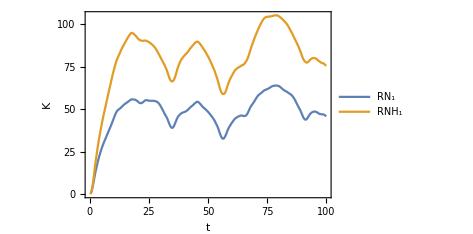

```mathematica
PRN1vsPRNH1=ListLinePlot[{KL5PRN1,KL5PRNH1}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\Text{RN})_(1)", TeXForm, HoldForm], Medium],Style[ToExpression["(\\Text{RNH})_1", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

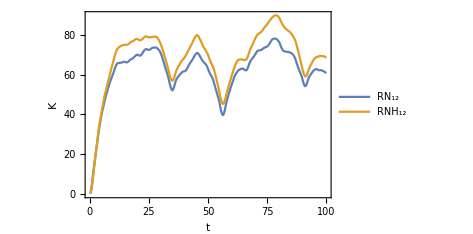

```mathematica
PRN12vsPRNH12=ListLinePlot[{KL5PRN12,KL5PRNH12}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\Text{RN})_(12)", TeXForm, HoldForm], Medium],Style[ToExpression["(\\Text{RNH})_{12}", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

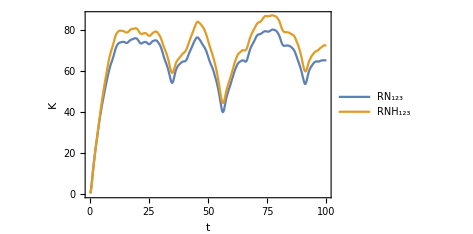

```mathematica
PRN123vsPRNH123=ListLinePlot[{KL5PRN123,KL5PRNH123}, AxesLabel->{"t","K"}, 
PlotLegends->Placed[{Style[ ToExpression["(\\Text{RN})_(123)", TeXForm, HoldForm], Medium],Style[ToExpression["(\\Text{RNH})_(123)", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

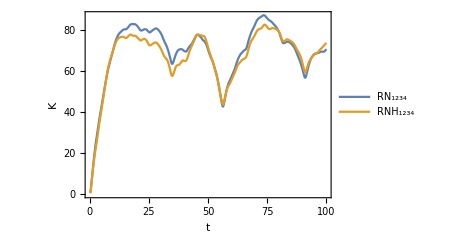

```mathematica
PRN1234vsPRNH1234=ListLinePlot[{KL5PRN1234,KL5PRNH1234}, AxesLabel->{"t","K"},
 PlotLegends->Placed[{Style[ ToExpression["(\\Text{RN})_(1234)", TeXForm, HoldForm], Medium],Style[ToExpression["(\\Text{RNH})_(1234)", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

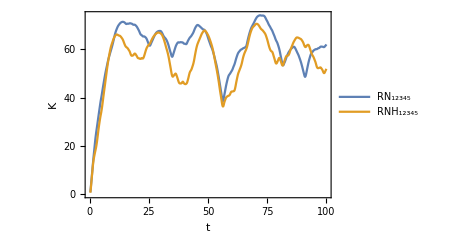

```mathematica
PRN12345vsPRNH12345=ListLinePlot[{KL5PRN12345,KL5PRNH12345}, AxesLabel->{"t","K"},
PlotLegends->Placed[{Style[ ToExpression["\\Text{RN}_(12345)", TeXForm, HoldForm], Medium],Style[ToExpression["(\\Text{RNH})_(12345)", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

### SITE-BY-SITE PLOTS

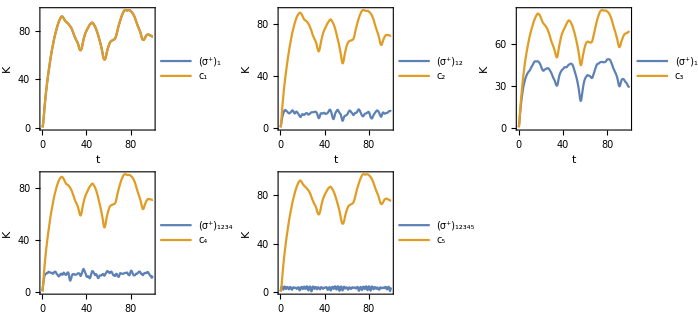

```mathematica
GraphicsGrid[{{Psp1vsPcc1,  Psp12vsPcc2,Psp123vsPcc3},{Psp1234vsPcc4,Psp12345vsPcc5}},ImageSize->Large]
```

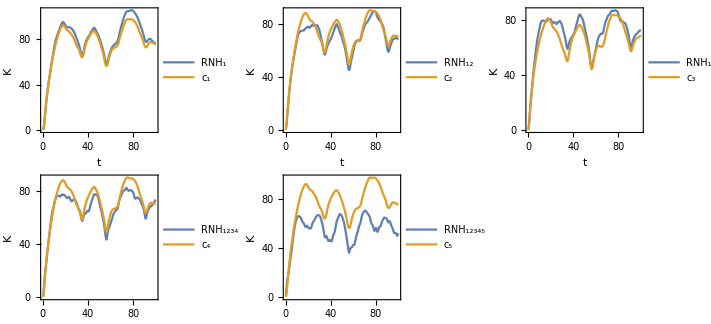

```mathematica
GraphicsGrid[{{PRNH1vsPcc1,PRNH12vsPcc2,PRNH123vsPcc3},{PRNH1234vsPcc4,PRNH12345vsPcc5}},ImageSize->Large]
```

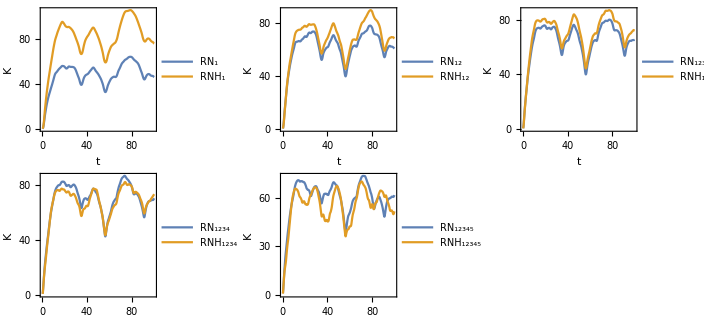

```mathematica
GraphicsGrid[{{PRN1vsPRNH1,PRN12vsPRNH12,PRN123vsPRNH123},{PRN1234vsPRNH1234,PRN12345vsPRNH12345}},ImageSize->Large]
```

## Open BC Comparisons

### Comparing σ^z operators as a function of sites

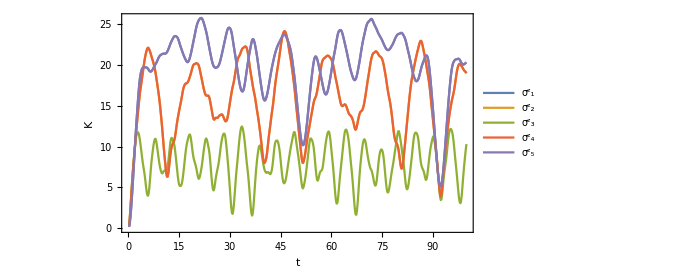

```mathematica
ListLinePlot[{KL5sz1,KL5sz2,KL5sz3,KL5sz4, KL5sz5},
AxesLabel->{"t","K"}, PlotLegends->Placed[{
Style[ ToExpression["(\\sigma^z)_(1)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^z)_(2)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^z)_(3)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^z)_(4)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^z)_(5)", TeXForm, HoldForm], Small]},Right],
Evaluate@Sequence@@FrameSpecsKtMulti]
```

### Comparing J-W operators as a function of sites

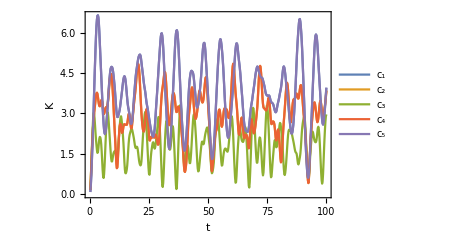

```mathematica
ListLinePlot[{KL5cc1,KL5cc2,KL5cc3,KL5cc4,KL5cc5},
AxesLabel->{"t","K"}, PlotLegends->Placed[{
Style[ ToExpression["(c)_(1)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c)_(2)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c)_(3)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c)_(4)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c)_(5)", TeXForm, HoldForm], Small]},Right],
Evaluate@Sequence@@FrameSpecsKt]
```

```mathematica
Rasterize[%,RasterSize->1300]
```

-Graphics-

### Comparing J-W operators in Ferromagnetic TFIM as a function of sites

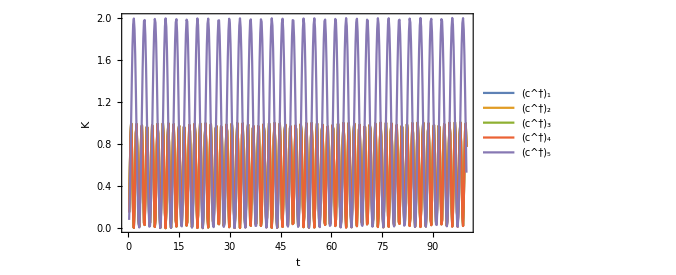

```mathematica
ListLinePlot[{KL5Ferrocc1,KL5Ferrocc2,KL5Ferrocc3, KL5Ferrocc4, KL5Ferrocc5},
AxesLabel->{"t","K"}, PlotLegends->Placed[{
Style[ ToExpression["(c^\\dagger)_(1)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c^\\dagger)_(2)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c^\\dagger)_(3)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c^\\dagger)_(4)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c^\\dagger)_(5)", TeXForm, HoldForm], Small]},Right(*{0.85,0.3}*)],
Evaluate@Sequence@@FrameSpecsKtMulti]
```

### Comparing multi-site sigma^+ ops as function of sites

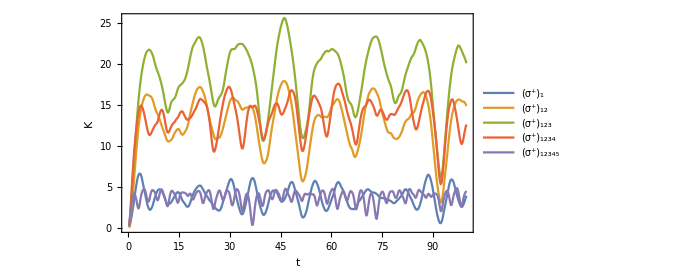

```mathematica
ListLinePlot[{KL5sp1,KL5sp12,KL5sp123,KL5sp1234, KL5sp12345},
AxesLabel->{"t","K"}, PlotLegends->Placed[{
Style[ ToExpression["(\\sigma^+)_(1)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(12)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(123)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(1234)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(12345)", TeXForm, HoldForm], Small]},Right],
Evaluate@Sequence@@FrameSpecsKtMulti]
```

### Comparing random normalized matrices as a function of sites

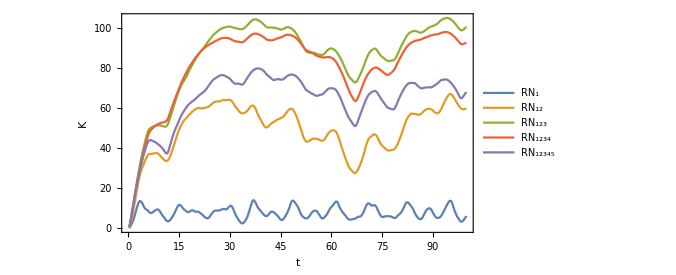

```mathematica
ListLinePlot[{KL5RN1,KL5RN12, KL5RN123, KL5RN1234, KL5RN12345},
AxesLabel->{"t","K"}, PlotLegends->Placed[{
Style[ ToExpression["(\\Text{RN})_(1)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\Text{RN})_(12)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\Text{RN})_(123)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\Text{RN})_(1234)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\Text{RN})_(12345)", TeXForm, HoldForm], Small]},Right],
Evaluate@Sequence@@FrameSpecsKtMulti]
```

### Comparing random normalized hermitian matrices as a function of sites

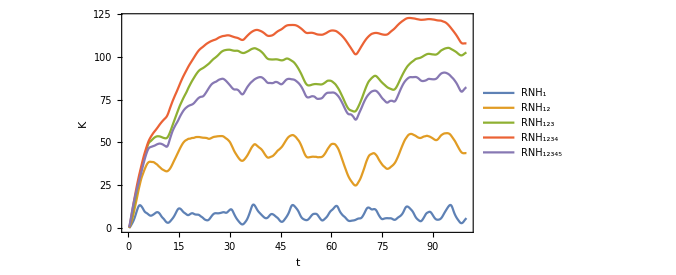

```mathematica
ListLinePlot[{KL5RNH1,KL5RNH12, KL5RNH123, KL5RNH1234, KL5RNH12345},
AxesLabel->{"t","K"}, PlotLegends->Placed[{
Style[ ToExpression["(\\Text{RNH})_(1)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\Text{RNH})_(12)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\Text{RNH})_(123)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\Text{RNH})_(1234)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\Text{RNH})_(12345)", TeXForm, HoldForm], Small]},Right],
Evaluate@Sequence@@FrameSpecsKtMulti]
```

### J-W vs σ^z (single-site)

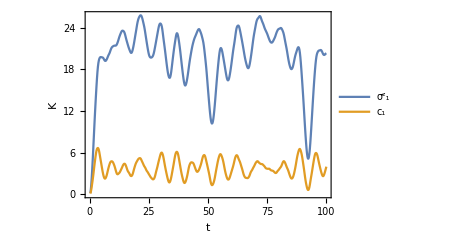

```mathematica
sz1vscc1=ListLinePlot[{KL5sz1,KL5cc1}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\sigma^z)_(1)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_1", TeXForm, HoldForm], Medium]},{0.7,0.35}],
Evaluate@Sequence@@FrameSpecsKt]
```

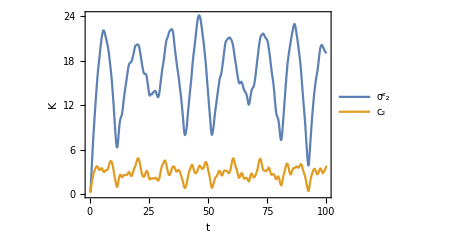

```mathematica
sz2vscc2=ListLinePlot[{KL5sz2,KL5cc2}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\sigma^z)_(2)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_2", TeXForm, HoldForm], Medium]},{0.7,0.35}],
Evaluate@Sequence@@FrameSpecsKt]
```

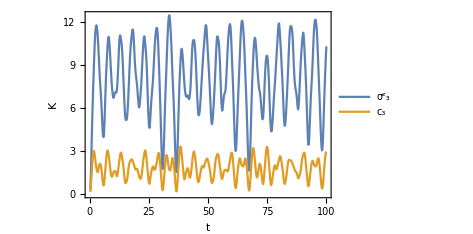

```mathematica
sz3vscc3=ListLinePlot[{KL5sz3,KL5cc3}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\sigma^z)_(3)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_3", TeXForm, HoldForm], Medium]},{0.5,0.3}],
Evaluate@Sequence@@FrameSpecsKt]
```

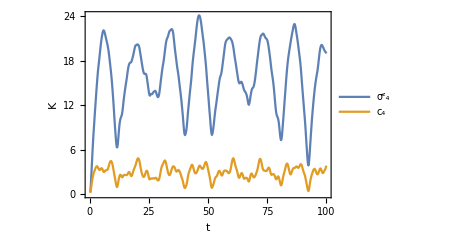

```mathematica
sz4vscc4=ListLinePlot[{KL5sz4,KL5cc4}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\sigma^z)_(4)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_4", TeXForm, HoldForm], Medium]},{0.7,0.35}],
Evaluate@Sequence@@FrameSpecsKt]
```

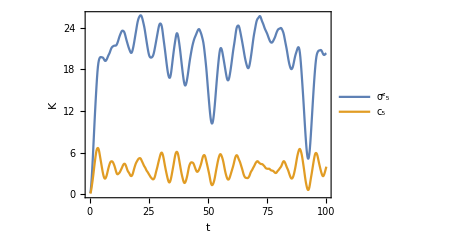

```mathematica
sz5vscc5=ListLinePlot[{KL5sz5,KL5cc5}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\sigma^z)_(5)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_5", TeXForm, HoldForm], Medium]},{0.7,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

### J-W vs σ^+ (multi-site)

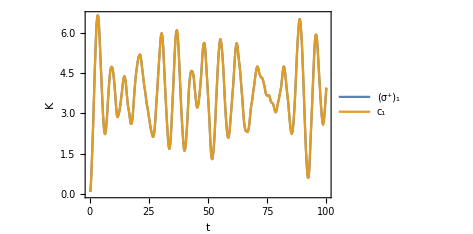

```mathematica
sp1vscc1=ListLinePlot[{KL5sp1,KL5cc1}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(1)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_1", TeXForm, HoldForm], Medium]},{0.75,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

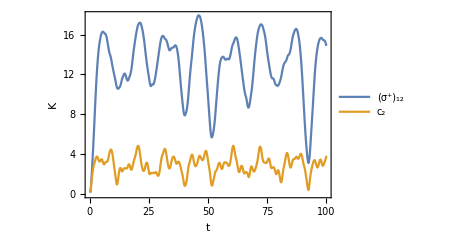

```mathematica
sp12vscc2=ListLinePlot[{KL5sp12,KL5cc2}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(12)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_2", TeXForm, HoldForm], Medium]},{0.75,0.39}],
Evaluate@Sequence@@FrameSpecsKt]
```

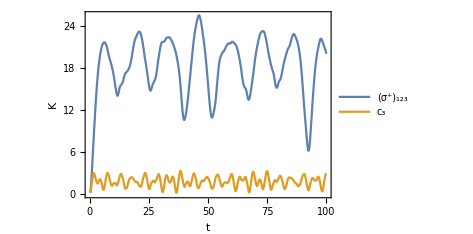

```mathematica
sp123vscc3=ListLinePlot[{KL5sp123,KL5cc3}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(123)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_3", TeXForm, HoldForm], Medium]},{0.75,0.3}],
Evaluate@Sequence@@FrameSpecsKt]
```

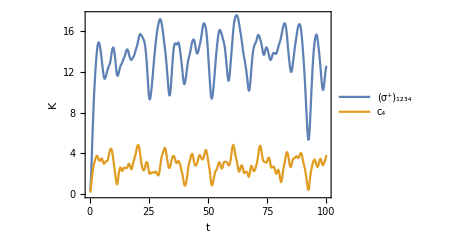

```mathematica
sp1234vscc4=ListLinePlot[{KL5sp1234,KL5cc4}, AxesLabel->{"t","K"},
 PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(1234)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_4", TeXForm, HoldForm], Medium]},{0.75,0.42}],
Evaluate@Sequence@@FrameSpecsKt]
```

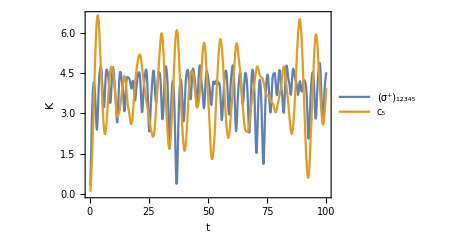

```mathematica
sp12345vscc5=ListLinePlot[{KL5sp12345,KL5cc5}, AxesLabel->{"t","K"},
 PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(12345)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_5", TeXForm, HoldForm], Medium]},{0.75,0.15}],
Evaluate@Sequence@@FrameSpecsKt]
```

### J-W vs σ^+ (single-site)

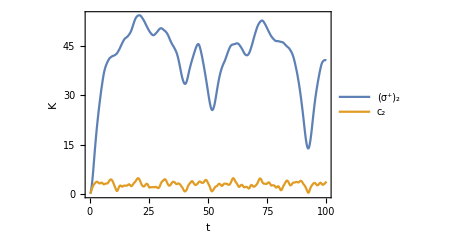

```mathematica
sp2vscc2=ListLinePlot[{KL5sp2,KL5cc2}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(2)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_2", TeXForm, HoldForm], Medium]},{0.7,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

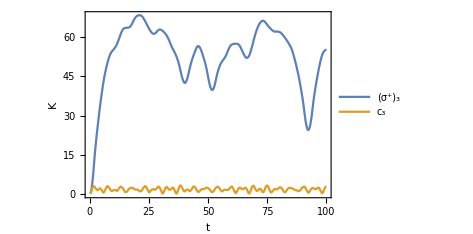

```mathematica
sp3vscc3=ListLinePlot[{KL5sp3,KL5cc3}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(3)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_3", TeXForm, HoldForm], Medium]},{0.7,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

```mathematica
sp4vscc4=ListLinePlot[{KL5sp4,KL5cc4}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(4)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_4", TeXForm, HoldForm], Medium]},{0.7,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

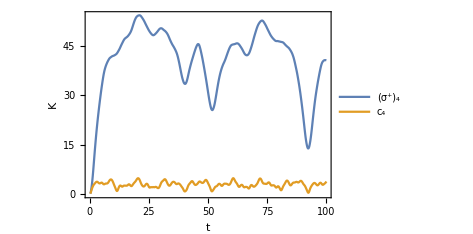

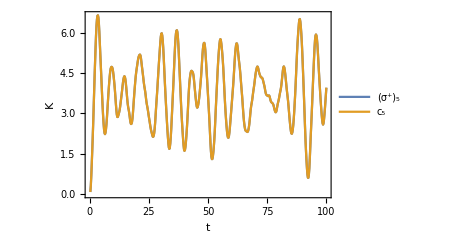

```mathematica
sp5vscc5=ListLinePlot[{KL5sp5,KL5cc5}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(5)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_5", TeXForm, HoldForm], Medium]},{0.7,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

### J-W vs random norm (multi-site)

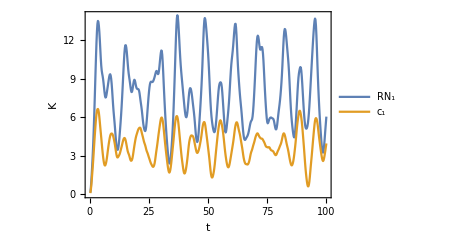

```mathematica
RN1vscc1=ListLinePlot[{KL5RN1,KL5cc1}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\Text{RN})_(1)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_1", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

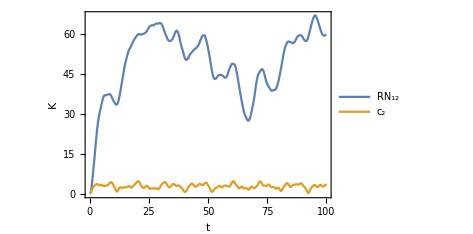

```mathematica
RN12vscc2=ListLinePlot[{KL5RN12,KL5cc2}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\Text{RN})_(12)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_2", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

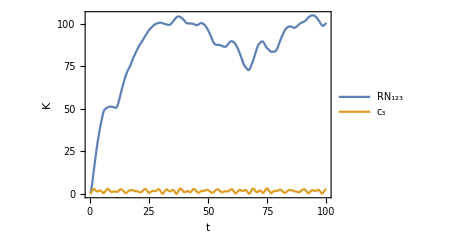

```mathematica
RN123vscc3=ListLinePlot[{KL5RN123,KL5cc3}, AxesLabel->{"t","K"}, 
PlotLegends->Placed[{Style[ ToExpression["(\\Text{RN})_(123)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_3", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

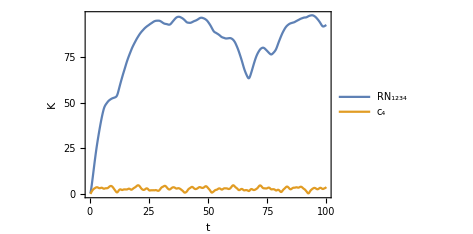

```mathematica
RN1234vscc4=ListLinePlot[{KL5RN1234,KL5cc4}, AxesLabel->{"t","K"},
 PlotLegends->Placed[{Style[ ToExpression["(\\Text{RN})_(1234)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_4", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

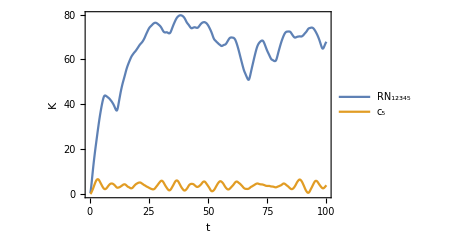

```mathematica
RN12345vscc5=ListLinePlot[{KL5RN12345,KL5cc5}, AxesLabel->{"t","K"},
 PlotLegends->Placed[{Style[ ToExpression["\\Text{RN}_(12345)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_5", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

### J-W vs random norm (single-site)

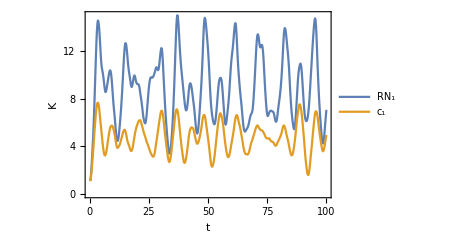

```mathematica
RN1vscc1=ListLinePlot[{KL5RN1,KL5cc1}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\Text{RN})_(1)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_1", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

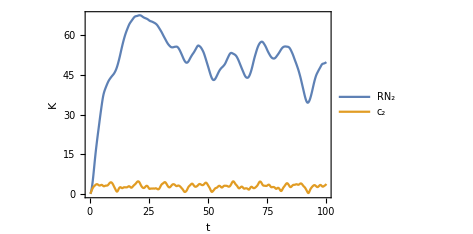

```mathematica
RN2vscc2=ListLinePlot[{KL5RN2,KL5cc2}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\Text{RN})_(2)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_2", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

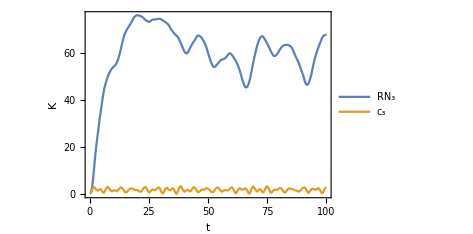

```mathematica
RN3vscc3=ListLinePlot[{KL5RN3,KL5cc3}, AxesLabel->{"t","K"}, 
PlotLegends->Placed[{Style[ ToExpression["(\\Text{RN})_(3)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_3", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

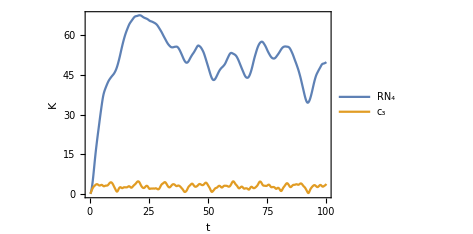

```mathematica
RN4vscc4=ListLinePlot[{KL5RN4,KL5cc4}, AxesLabel->{"t","K"}, 
PlotLegends->Placed[{Style[ ToExpression["(\\Text{RN})_(4)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_3", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

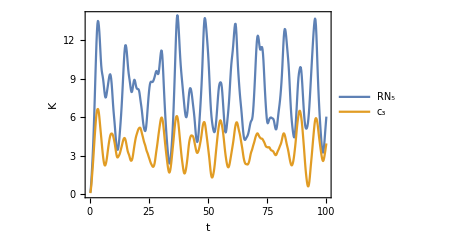

```mathematica
RN5vscc5=ListLinePlot[{KL5RN5,KL5cc5}, AxesLabel->{"t","K"}, 
PlotLegends->Placed[{Style[ ToExpression["(\\Text{RN})_(5)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_3", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

### J-W vs random norm hermitian (multi-site)

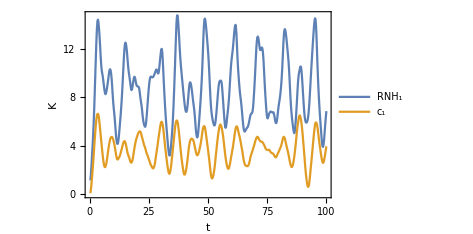

```mathematica
RNH1vscc1=ListLinePlot[{KL5RNH1,KL5cc1}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\Text{RNH})_(1)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_1", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

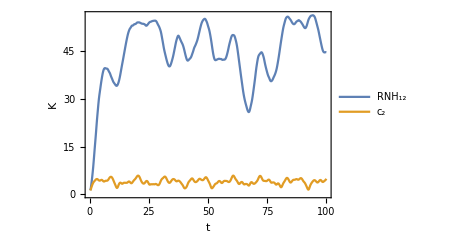

```mathematica
RNH12vscc2=ListLinePlot[{KL5RNH12,KL5cc2}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\Text{RNH})_(12)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_2", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

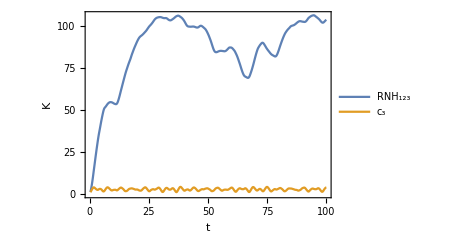

```mathematica
RNH123vscc3=ListLinePlot[{KL5RNH123,KL5cc3}, AxesLabel->{"t","K"}, 
PlotLegends->Placed[{Style[ ToExpression["(\\Text{RNH})_(123)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_3", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

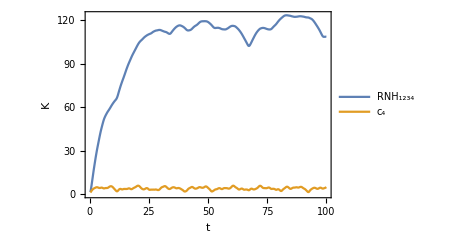

```mathematica
RNH1234vscc4=ListLinePlot[{KL5RNH1234,KL5cc4}, AxesLabel->{"t","K"},
 PlotLegends->Placed[{Style[ ToExpression["(\\Text{RNH})_(1234)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_4", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

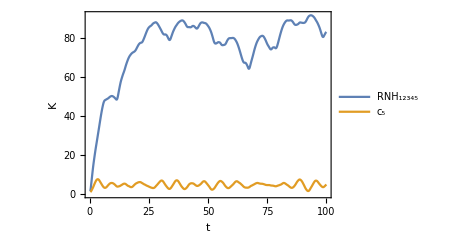

```mathematica
RNH12345vscc5=ListLinePlot[{KL5RNH12345,KL5cc5}, AxesLabel->{"t","K"},
 PlotLegends->Placed[{Style[ ToExpression["\\Text{RNH}_(12345)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_5", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

### J-W vs random norm hermitian (single-site)

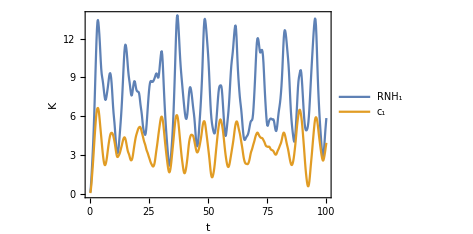

```mathematica
RNH1vscc1=ListLinePlot[{KL5RNH1,KL5cc1}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\Text{RNH})_(1)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_1", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

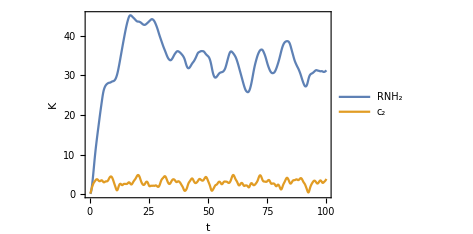

```mathematica
RNH2vscc2=ListLinePlot[{KL5RNH2,KL5cc2}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\Text{RNH})_(2)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_2", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

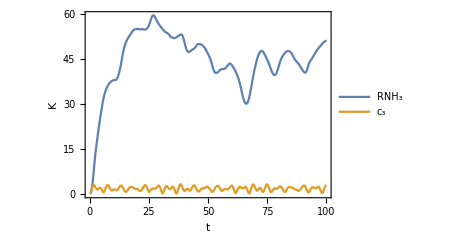

```mathematica
RNH3vscc3=ListLinePlot[{KL5RNH3,KL5cc3}, AxesLabel->{"t","K"}, 
PlotLegends->Placed[{Style[ ToExpression["(\\Text{RNH})_(3)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_3", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

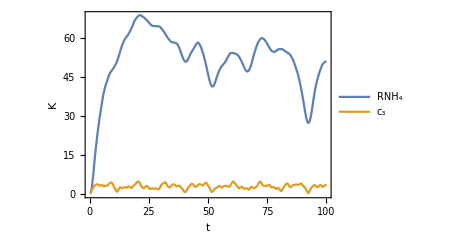

```mathematica
RNH4vscc4=ListLinePlot[{KL5RNH4,KL5cc4}, AxesLabel->{"t","K"}, 
PlotLegends->Placed[{Style[ ToExpression["(\\Text{RNH})_(4)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_3", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

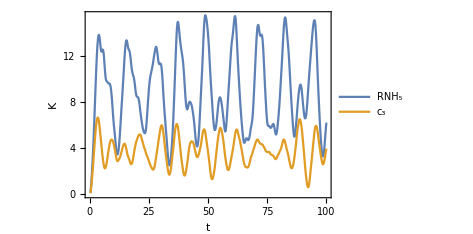

```mathematica
RNH5vscc5=ListLinePlot[{KL5RNH5,KL5cc5}, AxesLabel->{"t","K"}, 
PlotLegends->Placed[{Style[ ToExpression["(\\Text{RNH})_(5)", TeXForm, HoldForm], Medium],Style[ToExpression["(c)_3", TeXForm, HoldForm], Medium]},{0.8,0.25}],
Evaluate@Sequence@@FrameSpecsKt]
```

### SITE-BY-SITE PLOTS

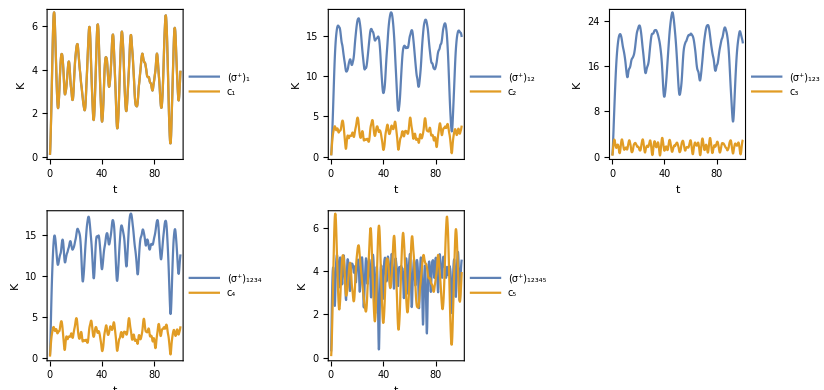

```mathematica
GraphicsGrid[{{sp1vscc1, sp12vscc2,sp123vscc3},{sp1234vscc4,sp12345vscc5}},ImageSize->Large]
```

Notes: The complexity for the multi-site sp operators relative to each other makes sense with multiplicity arguments - what we’d expect for multi-site operators. We can see that the J-W operators complexity isnt maximized when there are 3 non-id operators - this is significantly different to what we’d expect for multi-site operators.

The J-W operator also has a Z2 ‘end-to-end flip’ symmetry - naively not expected for such a non-local operator. I believe that this makes sense when you consider that there is an arbitrary choice in the string extending from the left or the right - and both choices correspond to identical operators on the dual chain. The existence of this symmetry for an operator could indicate the existence of a mapping to a local excitation in some dual representation.

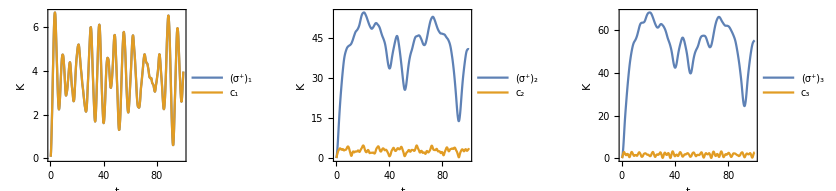

```mathematica
GraphicsGrid[{{sp1vscc1,sp2vscc2, sp3vscc3}},ImageSize->Large]
```

Notes: The complexity of the single-site sp operators increases when the excitation is closer to the middle. This is because the excitation has ‘2 directions’ to spread along the chain, and has this freedom for longer when its further from the boundaries. The complexity of the J-W operators dont change much for different sites. The fact that the Jordan-Wigner ‘tail’ is a σ^z operators, same as the Ising magnetic field, could explain that the one direction of spread is severely constrained. We can explore what happens if the magnetic field is weakened.

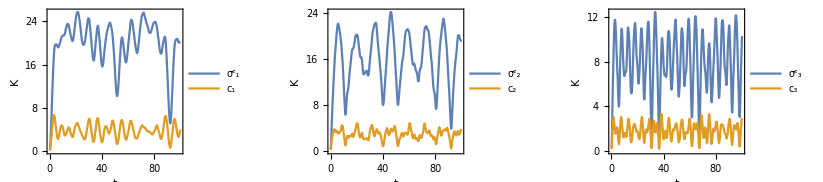

```mathematica
GraphicsGrid[{{sz1vscc1,sz2vscc2, sz3vscc3}},ImageSize->Large]
```

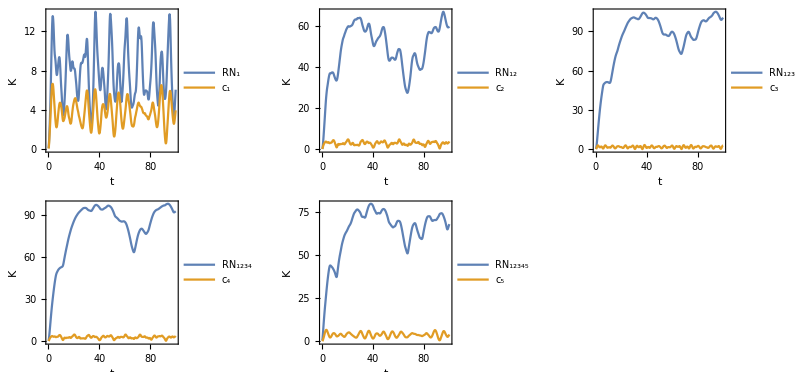

```mathematica
GraphicsGrid[{{RN1vscc1,RN12vscc2, RN123vscc3},{RN1234vscc4, RN12345vscc5}},ImageSize->Large]
```

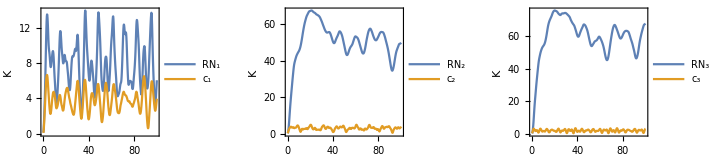

```mathematica
GraphicsGrid[{{RN1vscc1,RN2vscc2, RN3vscc3}},ImageSize->Large]
```

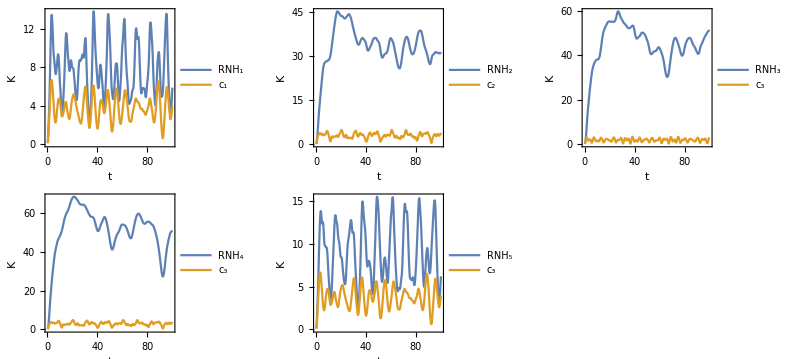

```mathematica
GraphicsGrid[{{RNH1vscc1,RNH2vscc2, RNH3vscc3},{ RNH4vscc4, RNH5vscc5}},ImageSize->Large]
```